```mathematica
ξ=ArcSinh[0.6]
fN = (4 π (-2 ξ Cosh[ξ]+(2+ξ^2) Sinh[ξ]))/ξ^3
```

0.568825

4.60329

```mathematica
dmax=4.0;
F[d_]:=NIntegrate[UnitStep[1-√(x^2+y^2+(z-d/2)^2)]UnitStep[1-√(x^2+y^2+(z+d/2)^2)],{x,-dmax,dmax},{y,-dmax,dmax},{z,-dmax,dmax}]
Fg[d_]:=NIntegrate[Cosh[ξ √(x^2+y^2+(z-d/2)^2)]Cosh[ξ √(x^2+y^2+(z+d/2)^2)]UnitStep[1-√(x^2+y^2+(z-d/2)^2)]UnitStep[1-√(x^2+y^2+(z+d/2)^2)],{x,-dmax,dmax},{y,-dmax,dmax},{z,-dmax,dmax}]
```

```mathematica
(* Plot[{F[d],Fg[d]},{d,0,dmax}] *)
```

```mathematica
nF=NIntegrate[(F[d]4π d^2)/(4/3 π)^2,{d,0,dmax}]
nFg=NIntegrate[(Fg[d]4π d^2)/fN^2,{d,0,dmax}]
```

NIntegrate::inumr: The integrand UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.

NIntegrate::inumr: The integrand Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.

```mathematica
FN[d_]:=(4π)/3(1-3/2 d/2+1/2(d/2)^3)UnitStep[1-d/2]
```

```mathematica
(* Plot[{F[d],FN[d]},{d,0,dmax}]*)
```

```mathematica
DF[r_,R_]:=1/((4/3 π)^2 R^3)F[r/R]
DFN[r_,R_]:=1/((4/3 π)^2 R^3)FN[r/R]
DFNg[r_,R_]:=1/(fN^2 R^3)Fg[r/R]
```

```mathematica
NIntegrate[DF[r,4.]4 Pi r^2,{r,0,8.0}]
NIntegrate[DFN[r,4.]4 Pi r^2,{r,0,8.0}]
NIntegrate[DFNg[r,4.]4 Pi r^2,{r,0,8.0}]
```

NIntegrate::inumr: The integrand UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.

1.

NIntegrate::inumr: The integrand Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.

```mathematica
RSPH=16.02;
RA=15.7;
RB=6.06;
RD=2.12799;
```

```mathematica
(* two gaussians *)
```

```mathematica
ASPH=197.0^3 3/4(2 Pi)^3 NIntegrate[1/((4 Pi RSPH^2)^(3/2))Exp[-r^2/(4 RSPH^2)] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,Infinity}]
AA=197.0^3 3/4(2 Pi)^3 NIntegrate[1/((4 Pi RA^2)^(3/2))Exp[-r^2/(4 RA^2)] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,Infinity}]
AB=197.0^3 3/4(2 Pi)^3 NIntegrate[1/((4 Pi RB^2)^(3/2))Exp[-r^2/(4 RB^2)] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,Infinity}]
```

7564.9

8028.35

120509.

```mathematica
NIntegrate[1/((4 Pi RB^2)^(3/2))Exp[-r^2/(4 RB^2)]4 Pi r^2,{r,0,Infinity}]
```

1.

```mathematica
(* random pairs in a sphere AND gaussian deuteron *)
```

```mathematica
ASPH=197.0^3 3/4(2 Pi)^3 NIntegrate[DFN[r,RSPH] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,2 RSPH}]
AA=197.0^3 3/4(2 Pi)^3 NIntegrate[DFN[r,RA] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,2 RA}]
AB=197.0^3 3/4(2 Pi)^3 NIntegrate[DFN[r,RB] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,2 RB}]
```

64239.2

67860.2

693463.

```mathematica
(* relativistic random pairs in a sphere AND gaussian deuteron *)
```

```mathematica
(* ASPH=197.0^3 3/4(2 Pi)^3 NIntegrate[DFNg[r,RSPH] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,2 RSPH}]
AA=197.0^3 3/4(2 Pi)^3 NIntegrate[DFNg[r,RA] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,2 RA}]
AB=197.0^3 3/4(2 Pi)^3 NIntegrate[DFNg[r,RB] 1/((4 Pi RD^2)^(3/2))Exp[-r^2/(4 RD^2)]4 Pi r^2,{r,0,2 RB}]*)
```

```mathematica
(* Hulthen wave function *)
```

```mathematica
φ[r_]:=√((α β (α+β))/(2π (α-β)^2))(Exp[-α r]-Exp[-β r])/r/.α->0.2/.β->1.56
Integrate[φ[r]^2 4 π r^2,{r,0,Infinity}]
```

1.

```mathematica
(* random pairs in a sphere AND Hulthen deuteron *)
```

```mathematica
ASPH=197.0^3 3/4(2 Pi)^3 NIntegrate[DFN[r,RSPH] φ[r]^2 4 Pi r^2,{r,0,2 RSPH}]
AA=197.0^3 3/4(2 Pi)^3 NIntegrate[DFN[r,RA] φ[r]^2 4 Pi r^2,{r,0,2 RA}]
AB=197.0^3 3/4(2 Pi)^3 NIntegrate[DFN[r,RB] φ[r]^2 4 Pi r^2,{r,0,2 RB}]
```

69660.5

73735.3

942476.

```mathematica
(* relativistic random pairs in a sphere AND Hulthen deuteron *)
```

```mathematica
ASPH=197.0^3 3/4(2 Pi)^3 NIntegrate[DFNg[r,RSPH] φ[r]^2 4 Pi r^2,{r,0,2 RSPH}]
AA=197.0^3 3/4(2 Pi)^3 NIntegrate[DFNg[r,RA] φ[r]^2 4 Pi r^2,{r,0,2 RA}]
AB=197.0^3 3/4(2 Pi)^3 NIntegrate[DFNg[r,RB] φ[r]^2 4 Pi r^2,{r,0,2 RB}]
```

NIntegrate::inumr: The integrand Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

68854.6

NIntegrate::inumr: The integrand Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

72870.6

NIntegrate::inumr: The integrand Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] Cosh[0.568825 √(x^2+y^2+(Times[«2»]+z)^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] UnitStep[1-√(x^2+y^2+Plus[«2»]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4.},{0,4.},{-4.,4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

926055.

```mathematica
H[r_,R_]:=1/(4/3 π R^3)(1-(3 r)/(4 R)+r^3/(16 R^3))UnitStep[1-r/(2 R)]
```

```mathematica
NIntegrate[DFN[r,5.0]4 Pi r^2,{r,0,15.0}]
```

1.

```mathematica
FN[d_]:=(4π)/3(1-3/2 d/2+1/2(d/2)^3)UnitStep[1-d/2]
DFN[r_,R_]:=1/((4/3 π)^2 R^3)FN[r/R]
NIntegrate[DFN[r,5.0]4 Pi r^2,{r,0,2 5.0}]
```

1.

```mathematica
(* flow parameters *)
```

```mathematica
Cosh[0.0225 6.06 1/0.197]
Tanh[0.0225 6.06 1/0.197]
```

1.24924

0.59935

```mathematica
Cosh[0.01 15.7 1/0.197]
Tanh[0.01 15.7 1/0.197]
```

1.33474

0.662331

```mathematica
Cosh[0.008 16.02 1/0.197]
Tanh[0.008 16.02 1/0.197]
```

1.21918

0.572046

```mathematica
Tanh[0.008 16 5.0]
```

0.5649

```mathematica
0.0225 6.06 5.0
```

0.68175

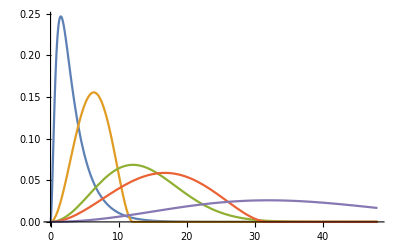

```mathematica
Plot[{φ[r]^2 4 Pi r^2,DFN[r,RB]4 Pi r^2,1/((4 Pi RB^2)^(3/2))Exp[-r^2/(4 RB^2)]4 Pi r^2,DFN[r,RSPH]4 Pi r^2,1/((4 Pi RSPH^2)^(3/2))Exp[-r^2/(4 RSPH^2)]4 Pi r^2,},{r,0,3 RSPH},PlotRange->All]
```